```mathematica
OutPutPath="ParralelD10";
SetDirectory[NotebookDirectory[]];
$P=2^31-1;
diffInvariants={mt2,s12,s123,s23,s234,s34,s345,s45,s56};
For[i=1,i<=9,i++,			
dhxbMatrices[diffInvariants[[i]]]=ReadList[FileNameJoin[{Directory[],ToString[StringForm["``/DEmatrix_d``",OutPutPath,diffInvariants[[i]]]]}]];
]
phasespacepoints=ReadList[FileNameJoin[{Directory[],ToString[StringForm["``/parameters",OutPutPath]]}]];
```

```mathematica
powerReconstruct[pars_,FitVecIn_]:=Module[{pars2,AnsatzPowersNumi,FitVec,AnsatzPowersDeno,MatNumiPart,onevc,parsCutOne,reconstructedFit,AnsatzPowersDenoOne,
fit,solrule,MatDenoPart,Solset,FinalMat,sol3,Ansatz,MaxPower},
	MaxPower=4;
AnsatzPowersNumi=FrobeniusSolve[{1,1},MaxPower];
	AnsatzPowersDeno=FrobeniusSolve[{1,1},MaxPower];
	pars2=pars/.{x_Integer:>{x,1}};
	(*MatNumiPart=Parallelize@Outer[m31ExpDot,pars2,AnsatzPowersNumi,1];*)

	MatNumiPart=Table[Table[Times@@PowerMod[pars2[[i]],AnsatzPowersNumi[[q]],$P],{q,1,Length[AnsatzPowersNumi]}],{i,1,Length[pars2]}];
	(*Table[Times@@PowerMod[pars2[[1]],AnsatzPowersNumi[[q]],$P],{q,1,Length[AnsatzPowersNumi]}]//Echo;*)
	
	FitVec=Expand[-FitVecIn,Modulus->$P];
	onevc=Table[{1},MaxPower+1];
	parsCutOne=MapThread[Join,{pars2,Transpose[{FitVec}]}];
	AnsatzPowersDenoOne=MapThread[Join,{AnsatzPowersDeno,onevc}];

	(*MatDenoPart=Parallelize@Outer[m31ExpDot,parsCutOne,AnsatzPowersDenoOne,1];*)
	
	MatDenoPart=Table[Table[Times@@PowerMod[parsCutOne[[i]],AnsatzPowersDenoOne[[j]],$P],{j,1,Length[AnsatzPowersDenoOne]}],{i,1,Length[parsCutOne]}];
	
	FinalMat=Expand[MapThread[Join,{MatNumiPart,MatDenoPart}],Modulus->$P];

	
	sol3=NullSpace[FinalMat,Modulus->$P];
	Ansatz=Sum[fac[n]t^n,{n,0,MaxPower}]/Sum[fac[n+MaxPower+1]t^n,{n,0,MaxPower}];
	Solset=Cases[Ansatz,fac[___],Infinity];
	solrule=Thread[Rule[Solset,sol3[[1]]]];
	fit=Together[Ansatz/.solrule]//ExpandDenominator//ExpandNumerator;
	Return[Expand[fit,Modulus->$P]]
]
```

```mathematica
LaunchKernels[20];
```

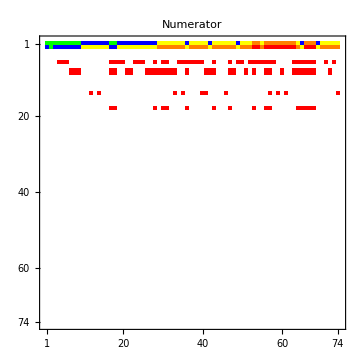
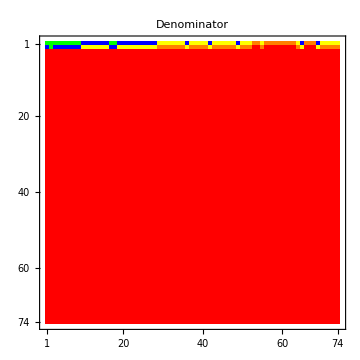
-Graphics- | -Graphics- |

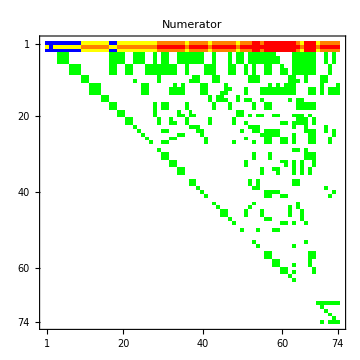
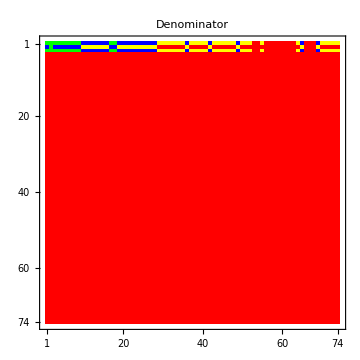
-Graphics- | -Graphics- |

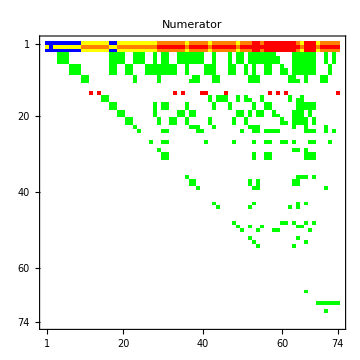
-Graphics- | -Graphics- |

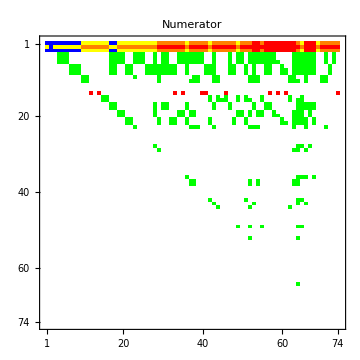
-Graphics- | -Graphics- |

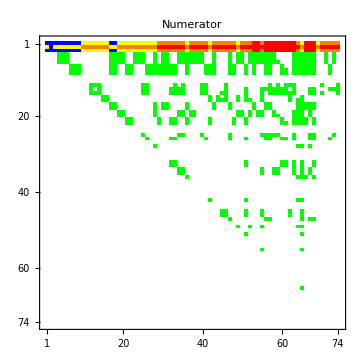
-Graphics- | -Graphics- |

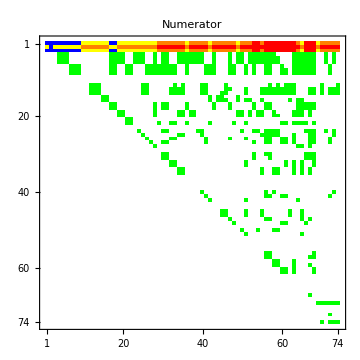
-Graphics- | -Graphics- |

-Graphics- | -Graphics- |

-Graphics- | -Graphics- |

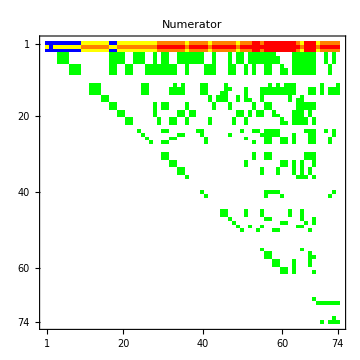
-Graphics- | -Graphics- |

```mathematica
colors={-1->White,0->Red,1->Green,2->Blue,3->Yellow,4->Orange,5->RGBColor["#e09f7d"],6->RGBColor["#EF5D60"],7->RGBColor["#EC4067"],8->RGBColor["#A01A7D"],9->RGBColor["#703399"],10->RGBColor["#0B050F"]};
CutsA=1;
CutsB=74;
For[i=1,i<=9,i++,
MatReco[diffInvariants[[i]]]=ParallelTable[Quiet[Expand[powerReconstruct[phasespacepoints[[All,1]],dhxbMatrices[diffInvariants[[i]]][[All,pos]]]/.{t->4-2ϵ},Modulus->$P]],{pos,1,Length[dhxbMatrices[s12][[1]]]}];
NumiPowers=Exponent[Numerator[MatReco[diffInvariants[[i]]]],ϵ]/.{-Infinity->-1};
DenoPowers=Exponent[Denominator[MatReco[diffInvariants[[i]]]],ϵ];
NumiPowersMat=NumiPowers//Normal;
DenoPowersMat=DenoPowers//Normal;
(*NonZerosPos=ReadList[FileNameJoin[{NotebookDirectory[],"files/NonZeroList.txt"}]];
NumiPowersMat=ConstantArray[-1,241^2];
NumiPowersMat[[NonZerosPos]]=NumiPowers;
DenoPowersMat=ConstantArray[-1,241^2];
DenoPowersMat[[NonZerosPos]]=DenoPowers;*)
P1=MatrixPlot[ArrayReshape[NumiPowersMat,{74,74}][[CutsA;;CutsB,CutsA;;CutsB]],ColorRules->colors,PlotLabel->"Numerator",ImageSize->Medium];
P2=MatrixPlot[ArrayReshape[DenoPowersMat,{74,74}][[CutsA;;CutsB,CutsA;;CutsB]],ColorRules->colors,PlotLabel->"Denominator",ImageSize->Medium];
L1=SwatchLegend[Values@colors[[2;;]],Keys@colors[[2;;]],LegendFunction->"Frame",LegendLayout->"Column",LegendLabel->diffInvariants[[i]]];
Print[Grid[{{P1,P2,L1}}]];
]
```

```mathematica
(*ArrayReshape[dhxbMatrices[diffInvariants[[2]]][[1]],{74,74}][[1,68]]
ArrayReshape[dhxbMatrices[diffInvariants[[2]]][[2]],{74,74}][[1,68]]
ArrayReshape[dhxbMatrices[diffInvariants[[2]]][[3]],{74,74}][[1,68]]

ArrayReshape[MatReco[diffInvariants[[2]]],{74,74}][[1,68]]
dhxbMatrices[diffInvariants[[2]]][[All,68]]
powerReconstruct[phasespacepoints[[All,1]],dhxbMatrices[diffInvariants[[6]]][[All,30]]]*)
(*ArrayReshape[MatReco[diffInvariants[[9]]],{74,74}][[22,22]]*)
pos=23;
ArrayReshape[MatReco[diffInvariants[[2]]],{74,74}][[pos,pos]]
ArrayReshape[MatReco[diffInvariants[[2]]],{74,74}]//MatrixForm
```

1007186279 ϵ

((1272413936+1618249575 ϵ+1003744509 ϵ^2)/(314100870+ϵ) | (876764470+691490622 ϵ+23407011 ϵ^2)/(314100870+ϵ) | (2053568396+681151527 ϵ+1457546993 ϵ^2)/(314100870+ϵ) | (970349200+1777307030 ϵ+1184761603 ϵ^2)/(314100870+ϵ) | (33994114+1316154337 ϵ+70385918 ϵ^2)/(314100870+ϵ) | (461745083+1190751471 ϵ+315724236 ϵ^2)/(314100870+ϵ) | (1417929825+70029330 ϵ+921404413 ϵ^2)/(314100870+ϵ) | (1265052177+134706729 ϵ+745965700 ϵ^2)/(314100870+ϵ) | (818521162+640809100 ϵ+2058516762 ϵ^2)/(314100870+ϵ) | (568702183+1694707600 ϵ+2087537851 ϵ^2+615139474 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (2018126335+440993314 ϵ+1979426223 ϵ^2+560052554 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (1987495084+1061690299 ϵ+989076271 ϵ^2+2125815604 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (703931813+1595672294 ϵ+693362469 ϵ^2+358536440 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (1678803567+79500557 ϵ+336705062 ϵ^2+2046985804 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (456360846+1781947448 ϵ+424355479 ϵ^2+1857873166 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (1976044907+1408441976 ϵ+2114804703 ϵ^2+713765512 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (2009389388+915499983 ϵ+916639509 ϵ^2)/(314100870+ϵ) | (76372976+675219711 ϵ+839010887 ϵ^2)/(314100870+ϵ) | (1668471868+688215116 ϵ+1839791208 ϵ^2+696516687 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (231271256+1392766469 ϵ+1293898199 ϵ^2+900705417 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (541847416+722271646 ϵ+759001188 ϵ^2+1563539466 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (666977865+1079455326 ϵ+1672583928 ϵ^2+637972727 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (1829295379+954185082 ϵ+1502657444 ϵ^2+244327077 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (1079106582+1947464561 ϵ+1765866415 ϵ^2+862224496 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (1861978626+1804446950 ϵ+1730542541 ϵ^2+855845717 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (216131717+228588039 ϵ+1646252733 ϵ^2+995028431 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (1799735458+287032305 ϵ+426718020 ϵ^2+1381242341 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (1264522275+957613748 ϵ+776287041 ϵ^2+1396671690 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (1491588521+134887266 ϵ+693321435 ϵ^2+586214255 ϵ^3+1447818151 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (1159582745+1026150546 ϵ+886628969 ϵ^2+2023971182 ϵ^3+1066151002 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (292694167+729672454 ϵ+1087625580 ϵ^2+549608702 ϵ^3+1593280518 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (713856915+419297135 ϵ+2018412010 ϵ^2+1862766584 ϵ^3+1536713976 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (419994193+1127543613 ϵ+852643207 ϵ^2+524307511 ϵ^3+1453287484 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (1928369347+22944618 ϵ+243458928 ϵ^2+2009151573 ϵ^3+1221764861 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (84100012+696959433 ϵ+786998189 ϵ^2+6208326 ϵ^3+405365094 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (692004848+884941317 ϵ+277004311 ϵ^2+529540299 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (1212634054+372293903 ϵ+1449306795 ϵ^2+327077140 ϵ^3+2056064945 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (1869125001+1752584899 ϵ+572165021 ϵ^2+1048529603 ϵ^3+274174501 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (1134927638+89877031 ϵ+1150106307 ϵ^2+466923080 ϵ^3+1533739513 ϵ^4)/(157050435+602590519 ϵ+1387842692 ϵ^2+ϵ^3) | (467768192+917605035 ϵ+1423683353 ϵ^2+1599179658 ϵ^3+96320083 ϵ^4)/(157050435+602590519 ϵ+1387842692 ϵ^2+ϵ^3) | (151517255+1500610402 ϵ+2064389603 ϵ^2+101532155 ϵ^3+1602448113 ϵ^4)/(157050435+602590519 ϵ+1387842692 ϵ^2+ϵ^3) | (173799861+114028654 ϵ+911863431 ϵ^2+462700789 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (434378211+86972482 ϵ+40005618 ϵ^2+1165930185 ϵ^3+594547541 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (926236511+1201248402 ϵ+1181078943 ϵ^2+486380219 ϵ^3+2068692853 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (40071943+1728764380 ϵ+867276468 ϵ^2+1044598073 ϵ^3+1578094089 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (500831053+1113924519 ϵ+396119818 ϵ^2+696205497 ϵ^3+1883797141 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (1038679116+909304520 ϵ+1723828049 ϵ^2+107881313 ϵ^3+434631653 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (495498251+410969766 ϵ+633543806 ϵ^2+228455313 ϵ^3+1424821718 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (1193837648+1102209931 ϵ+1294371880 ϵ^2+1907847254 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (2142521318+1775375733 ϵ+824703725 ϵ^2+1228585206 ϵ^3+66126479 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (1709723319+537252310 ϵ+1042631833 ϵ^2+1195647629 ϵ^3+1447551426 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (1301958251+688573217 ϵ+1925246248 ϵ^2+1609983877 ϵ^3+1681531003 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | 1 | 1 | (1625328274+1377759420 ϵ+330298094 ϵ^2+61813313 ϵ^3+1490708838 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | (1195476452+719728293 ϵ+36330968 ϵ^2+439384338 ϵ^3+1078998492 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (1842328440+1559964884 ϵ+1875168095 ϵ^2+1529245956 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | 1 | 1 | 1 | (1548764275+1097807544 ϵ+2037779828 ϵ^2+19465208 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (344418007+746681018 ϵ+889187793 ϵ^2+2057424708 ϵ^3+1085425828 ϵ^4)/(157050435+602590519 ϵ+1387842692 ϵ^2+ϵ^3) | (122492624+655303423 ϵ+1324442301 ϵ^2+1753463879 ϵ^3+2137518961 ϵ^4)/(157050435+602590519 ϵ+1387842692 ϵ^2+ϵ^3) | (1934182854+760974387 ϵ+1819503502 ϵ^2+1301249737 ϵ^3+1311071540 ϵ^4)/(157050435+602590519 ϵ+1387842692 ϵ^2+ϵ^3) | (1647889769+1329464386 ϵ+128404432 ϵ^2+776720345 ϵ^3+1503556467 ϵ^4)/(157050435+602590519 ϵ+1387842692 ϵ^2+ϵ^3) | (1099273067+497401921 ϵ+280028014 ϵ^2+1307186658 ϵ^3+2113206653 ϵ^4)/(157050435+602590519 ϵ+1387842692 ϵ^2+ϵ^3)
(164670735+857540193 ϵ+1133058799 ϵ^2+529736176 ϵ^3)/(157050435+1387842694 ϵ+ϵ^2) | (732052416+666858890 ϵ+723454500 ϵ^2)/(314100870+ϵ) | (912446075+1850352133 ϵ+2091908139 ϵ^2+362417986 ϵ^3)/(157050435+1387842694 ϵ+ϵ^2) | (1692702237+858839539 ϵ+1553258087 ϵ^2+1388359363 ϵ^3)/(157050435+1387842694 ϵ+ϵ^2) | (1729878567+1467617251 ϵ+1696327991 ϵ^2+748213621 ϵ^3)/(157050435+1387842694 ϵ+ϵ^2) | (2024447465+299467292 ϵ+869124817 ϵ^2+738719329 ϵ^3)/(157050435+1387842694 ϵ+ϵ^2) | (434764134+2103734041 ϵ+1513511998 ϵ^2+836352171 ϵ^3)/(157050435+1387842694 ϵ+ϵ^2) | (211141705+1997937692 ϵ+98120893 ϵ^2+1660715739 ϵ^3)/(157050435+1387842694 ϵ+ϵ^2) | (98023235+673956176 ϵ+896603872 ϵ^2+1991196240 ϵ^3)/(157050435+1387842694 ϵ+ϵ^2) | (1319744499+268090393 ϵ+1030328485 ϵ^2+585938488 ϵ^3+246625871 ϵ^4)/(995216606+1610612735 ϵ+314100870 ϵ^2+ϵ^3) | (1519482049+1088515227 ϵ+466794539 ϵ^2+197398985 ϵ^3+835632764 ϵ^4)/(995216606+1610612735 ϵ+314100870 ϵ^2+ϵ^3) | (631635019+493579918 ϵ+1069438434 ϵ^2+1629335955 ϵ^3+1964349162 ϵ^4)/(995216606+1610612735 ϵ+314100870 ϵ^2+ϵ^3) | (30187574+1192810954 ϵ+946325433 ϵ^2+1788533719 ϵ^3+1868592586 ϵ^4)/(995216606+1610612735 ϵ+314100870 ϵ^2+ϵ^3) | (640068917+241204149 ϵ+767936110 ϵ^2+1749104799 ϵ^3+325973436 ϵ^4)/(995216606+1610612735 ϵ+314100870 ϵ^2+ϵ^3) | (73304026+1678388014 ϵ+812072391 ϵ^2+1716761315 ϵ^3+147073144 ϵ^4)/(2095133502+410264086 ϵ+2103670576 ϵ^2+ϵ^3) | (740590930+1434940148 ϵ+570902208 ϵ^2+1637406820 ϵ^3+1149354144 ϵ^4)/(2095133502+410264086 ϵ+2103670576 ϵ^2+ϵ^3) | (1867419476+929173148 ϵ+1916291952 ϵ^2+1262354064 ϵ^3)/(157050435+1387842694 ϵ+ϵ^2) | (1219830807+1155084513 ϵ+900655960 ϵ^2+8055797 ϵ^3)/(157050435+1387842694 ϵ+ϵ^2) | (1895803353+251612513 ϵ+513118422 ϵ^2+495341489 ϵ^3+57495186 ϵ^4)/(2095133502+410264086 ϵ+2103670576 ϵ^2+ϵ^3) | (1401602626+1075194098 ϵ+819568459 ϵ^2+1501989315 ϵ^3+639146754 ϵ^4)/(2095133502+410264086 ϵ+2103670576 ϵ^2+ϵ^3) | (1797059914+1306911240 ϵ+153316132 ϵ^2+273355240 ϵ^3+997530631 ϵ^4)/(2095133502+410264086 ϵ+2103670576 ϵ^2+ϵ^3) | (810923546+1670265878 ϵ+371799870 ϵ^2+1627316382 ϵ^3+1203638832 ϵ^4)/(2095133502+410264086 ϵ+2103670576 ϵ^2+ϵ^3) | (1591864995+87251934 ϵ+607415695 ϵ^2+1877196141 ϵ^3+1696584670 ϵ^4)/(995216606+1610612735 ϵ+314100870 ϵ^2+ϵ^3) | (1899821732+211742514 ϵ+1055979346 ϵ^2+1082425506 ϵ^3+754829498 ϵ^4)/(995216606+1610612735 ϵ+314100870 ϵ^2+ϵ^3) | (857033520+1027962922 ϵ+2017984558 ϵ^2+1088306804 ϵ^3+14409644 ϵ^4)/(995216606+1610612735 ϵ+314100870 ϵ^2+ϵ^3) | (420661047+1657456104 ϵ+336050468 ϵ^2+234961298 ϵ^3+2018242038 ϵ^4)/(995216606+1610612735 ϵ+314100870 ϵ^2+ϵ^3) | (623249826+632138848 ϵ+412171610 ϵ^2+954887478 ϵ^3+1523968405 ϵ^4)/(995216606+1610612735 ϵ+314100870 ϵ^2+ϵ^3) | (500110783+1427130394 ϵ+573560651 ϵ^2+496825384 ϵ^3+1105092984 ϵ^4)/(2095133502+410264086 ϵ+2103670576 ϵ^2+ϵ^3) | 1 | 1 | 1 | 1 | 1 | 1 | 1 | (337543352+1492106240 ϵ+142745566 ϵ^2+585063069 ϵ^3+473690968 ϵ^4)/(2095133502+410264086 ϵ+2103670576 ϵ^2+ϵ^3) | 1 | 1 | 1 | 1 | 1 | (1665992961+2139362883 ϵ+743182897 ϵ^2+1155221744 ϵ^3+1244390940 ϵ^4)/(2095133502+410264086 ϵ+2103670576 ϵ^2+ϵ^3) | 1 | 1 | 1 | 1 | 1 | 1 | (1008694003+1132651542 ϵ+700066366 ϵ^2+1216807311 ϵ^3+1039980652 ϵ^4)/(2095133502+410264086 ϵ+2103670576 ϵ^2+ϵ^3) | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | (659813132+802129104 ϵ+1888286799 ϵ^2+340310200 ϵ^3+1247683312 ϵ^4)/(2095133502+410264086 ϵ+2103670576 ϵ^2+ϵ^3) | 1 | 1 | 1 | (518136014+1562226188 ϵ+1114880877 ϵ^2+1074595472 ϵ^3+2146603562 ϵ^4)/(995216606+1610612735 ϵ+314100870 ϵ^2+ϵ^3) | 1 | 1 | 1 | 1 | 1
(1742487215 ϵ+993926373 ϵ^2)/(314100870+ϵ) | (1544976387 ϵ+942469127 ϵ^2)/(314100870+ϵ) | (1748636293 ϵ+759869579 ϵ^2)/(314100870+ϵ) | (222897924 ϵ+1293069590 ϵ^2)/(314100870+ϵ) | (1301753307 ϵ+281956514 ϵ^2)/(314100870+ϵ) | (2088595024 ϵ+893522211 ϵ^2)/(314100870+ϵ) | (1958737518 ϵ+875955065 ϵ^2)/(314100870+ϵ) | (1420012527 ϵ+1624138093 ϵ^2)/(314100870+ϵ) | (337043590 ϵ+931771941 ϵ^2)/(314100870+ϵ) | (1791181246 ϵ+1514797470 ϵ^2+619050299 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (1162459066 ϵ+555572952 ϵ^2+1095496384 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (1448520416 ϵ+370022009 ϵ^2+739007409 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (1527367116 ϵ+1278261360 ϵ^2+2056758638 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (1933344299 ϵ+1682326801 ϵ^2+1798011546 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (1493842080 ϵ+304311163 ϵ^2+1553158493 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (2114853050 ϵ+680824714 ϵ^2+140034887 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (1764834019 ϵ+1538874683 ϵ^2)/(314100870+ϵ) | (1520120675 ϵ+1241254814 ϵ^2)/(314100870+ϵ) | (1062854164 ϵ+954567530 ϵ^2+850716418 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (514972729 ϵ+1082621604 ϵ^2+419125628 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (613387922 ϵ+912048544 ϵ^2+43334507 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (1672169933 ϵ+1326409295 ϵ^2+1232607907 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (448536252 ϵ+1520301622 ϵ^2+88336735 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (1698044867 ϵ+2000722219 ϵ^2+2055645068 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (1324625584 ϵ+403910791 ϵ^2+1141532784 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (2121018878 ϵ+221123795 ϵ^2+1825949043 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (1353856031 ϵ+919963633 ϵ^2+662006258 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (1924955068 ϵ+1792934716 ϵ^2+866807794 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (497363551 ϵ+365372376 ϵ^2+1352354180 ϵ^3+695529394 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (505861974 ϵ+337749586 ϵ^2+1769383505 ϵ^3+2110090298 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (1737871428 ϵ+1104520010 ϵ^2+1581187911 ϵ^3+397832391 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (55155812 ϵ+1944572973 ϵ^2+1889197531 ϵ^3+1202846008 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (1818719852 ϵ+98613891 ϵ^2+88775442 ϵ^3+2100934494 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (368622237 ϵ+462514964 ϵ^2+120962671 ϵ^3+1496161427 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (1410552176 ϵ+941091602 ϵ^2+2115893667 ϵ^3+1288588240 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (1333755339 ϵ+1882776679 ϵ^2+541784082 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (775568060 ϵ+1058797543 ϵ^2+773022904 ϵ^3+2044162161 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (242604216 ϵ+1428615257 ϵ^2+1206273030 ϵ^3+1334125406 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (248297726 ϵ+512031465 ϵ^2+1804541645 ϵ^3+356156074 ϵ^4)/(157050435+602590519 ϵ+1387842692 ϵ^2+ϵ^3) | (1882210065 ϵ+2068119244 ϵ^2+51887824 ϵ^3+1451108246 ϵ^4)/(157050435+602590519 ϵ+1387842692 ϵ^2+ϵ^3) | (2111465198 ϵ+1052276864 ϵ^2+1910509426 ϵ^3+1718685724 ϵ^4)/(157050435+602590519 ϵ+1387842692 ϵ^2+ϵ^3) | (2054319922 ϵ+1415423490 ϵ^2+260258042 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (1749267360 ϵ+584787704 ϵ^2+705771574 ϵ^3+636255186 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (328625596 ϵ+324562370 ϵ^2+1423804870 ϵ^3+282145518 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (100612126 ϵ+2070553593 ϵ^2+66529595 ϵ^3+1527026607 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (959507371 ϵ+421883834 ϵ^2+1033587297 ϵ^3+463548323 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (1939106997 ϵ+295057994 ϵ^2+974968824 ϵ^3+1852465704 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (1232563087 ϵ+434811412 ϵ^2+28220734 ϵ^3+695041615 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (1078323946 ϵ+1236904204 ϵ^2+1992397351 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | (1039413500 ϵ+1470841252 ϵ^2+1480398360 ϵ^3+1154456707 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (816694865 ϵ+1590990128 ϵ^2+1738164232 ϵ^3+1674836647 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (1036174110 ϵ+1003184158 ϵ^2+1825171803 ϵ^3+1320004467 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | 1 | 1 | (1867730561 ϵ+2106407940 ϵ^2+1061963744 ϵ^3+594205405 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | (816491296 ϵ+1990317202 ϵ^2+1586946825 ϵ^3+404589430 ϵ^4)/(52350145+1527818981 ϵ+2103670575 ϵ^2+ϵ^3) | (756480991 ϵ+1263282367 ϵ^2+893184357 ϵ^3)/(2042783357+1029928752 ϵ+ϵ^2) | 1 | 1 | 1 | (9633399 ϵ+1154401689 ϵ^2+1338102709 ϵ^3)/(1990433212+1387842693 ϵ+ϵ^2) | (574771603 ϵ+1316492331 ϵ^2+1300948300 ϵ^3+1307579209 ϵ^4)/(157050435+602590519 ϵ+1387842692 ϵ^2+ϵ^3) | (446679404 ϵ+70758229 ϵ^2+121011344 ϵ^3+732744298 ϵ^4)/(157050435+602590519 ϵ+1387842692 ϵ^2+ϵ^3) | (1487356763 ϵ+226720292 ϵ^2+2085016783 ϵ^3+1321697625 ϵ^4)/(157050435+602590519 ϵ+1387842692 ϵ^2+ϵ^3) | (249943308 ϵ+1247596931 ϵ^2+828697788 ϵ^3+2095941694 ϵ^4)/(157050435+602590519 ϵ+1387842692 ϵ^2+ϵ^3) | (793647923 ϵ+986471901 ϵ^2+1601132884 ϵ^3+1614596096 ϵ^4)/(157050435+602590519 ϵ+1387842692 ϵ^2+ϵ^3)
0 | 0 | 0 | 180518684 ϵ | 924071252 ϵ | 1238747609 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 288130742 ϵ | 38298410 ϵ | 349289354 ϵ | 381202393 ϵ | 0 | 0 | 1712710999 ϵ | 1245831874 ϵ | 307279032 ϵ | 0 | 0 | 1379616047 ϵ | 0 | 626703853 ϵ | 222380066 ϵ | 0 | 0 | 1630107289 ϵ | 339330801 ϵ | 1676784100 ϵ | 888402198 ϵ | 1622639926 ϵ | 1872415620 ϵ | 1196399913 ϵ | 0 | 0 | 1107774301 ϵ | 0 | 0 | 0 | 1451043827 ϵ | 0 | 1016068029 ϵ | 703251591 ϵ | 0 | 520610304 ϵ | 1882876730 ϵ | 572952484 ϵ | 406954296 ϵ | 670132242 ϵ | 1244112879 ϵ | 678661602 ϵ | 0 | 0 | 0 | 0 | 710356641 ϵ | 126290457 ϵ | 2129089650 ϵ | 1756666620 ϵ | 2078053780 ϵ | 1402603185 ϵ | 0 | 0 | 1557408537 ϵ | 0 | 1332126790 ϵ | 0
0 | 0 | 0 | 2014994663 ϵ | 931977877 ϵ | 277550655 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 834298233 ϵ | 1147667815 ϵ | 1284471010 ϵ | 661711222 ϵ | 0 | 0 | 1586119086 ϵ | 84398656 ϵ | 144553183 ϵ | 0 | 0 | 920247641 ϵ | 0 | 544669649 ϵ | 157679310 ϵ | 0 | 0 | 1188974256 ϵ | 533854862 ϵ | 710040535 ϵ | 1311468263 ϵ | 1437149349 ϵ | 138217649 ϵ | 91936607 ϵ | 0 | 0 | 359408825 ϵ | 0 | 0 | 0 | 1072254443 ϵ | 0 | 1756049080 ϵ | 558292458 ϵ | 0 | 1403398559 ϵ | 1264245401 ϵ | 1388460512 ϵ | 1626482268 ϵ | 1976937581 ϵ | 1119737158 ϵ | 1455461668 ϵ | 1965402461 ϵ | 0 | 0 | 0 | 886813734 ϵ | 634537440 ϵ | 1050320263 ϵ | 1484819478 ϵ | 782602029 ϵ | 1446304905 ϵ | 0 | 0 | 1020265308 ϵ | 0 | 1833136083 ϵ | 0
0 | 0 | 0 | 201842719+1583821905 ϵ | 602858717+227600988 ϵ | 1098474494+1708754395 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 682618524+123147959 ϵ | 1057425793+1217251505 ϵ | 586303985+2134712682 ϵ | 1594129113+556823117 ϵ | 0 | 0 | 1071797185+1512815167 ϵ | 1386627149+574537404 ϵ | 98758004+345942608 ϵ | 0 | 0 | 583408373+2109149768 ϵ | 0 | 1417710843+1530402291 ϵ | 2141254348+2002683906 ϵ | 0 | 0 | 950074827+525614258 ϵ | 461720731+302868744 ϵ | 1665251780+131086142 ϵ | 1784631053+1369227040 ϵ | 318409976+631683638 ϵ | 391061523+1076960387 ϵ | 14475782+1274650001 ϵ | 0 | 0 | 621616830+911030240 ϵ | 0 | 0 | 0 | 25474572+445650472 ϵ | 0 | 602467073+2091885006 ϵ | 1808023770+1868530742 ϵ | 0 | 1063909735+1471271794 ϵ | 1126010648+1655970778 ϵ | 955229928+1452686801 ϵ | 1477887671+722270559 ϵ | 393205560+908929223 ϵ | 190039313+966436552 ϵ | 923441462+16391421 ϵ | 344813980 ϵ | 0 | 0 | 0 | 1048942964+581247627 ϵ | 1406668357+196427744 ϵ | 432770943+211071235 ϵ | 1669717341+362613755 ϵ | 474905758+1839078693 ϵ | 701171224+1171504238 ϵ | 0 | 0 | 939336262+1249533600 ϵ | 0 | 235108204+928280413 ϵ | 0
0 | 0 | 0 | 0 | 0 | 0 | 1894822738 ϵ | 178623237 ϵ | 51206405 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1467754586 ϵ | 2147255381 ϵ | 0 | 0 | 651163930 ϵ | 1803477439 ϵ | 0 | 0 | 0 | 1410373951 ϵ | 322288612 ϵ | 1529521848 ϵ | 754621354 ϵ | 293722818 ϵ | 1398974412 ϵ | 1971288681 ϵ | 788377872 ϵ | 0 | 0 | 1132999297 ϵ | 0 | 0 | 0 | 0 | 655065578 ϵ | 2051154038 ϵ | 981788019 ϵ | 0 | 0 | 0 | 1462927141 ϵ | 326777480 ϵ | 0 | 0 | 1770918841 ϵ | 0 | 433913648 ϵ | 0 | 0 | 903560113 ϵ | 1842208106 ϵ | 0 | 0 | 1576755744 ϵ | 0 | 0 | 2071301555 ϵ | 164253280 ϵ | 1438498984 ϵ | 317436055 ϵ | 779745734 ϵ | 1920032105 ϵ | 0 | 0 | 0 | 1561601195 ϵ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1289420409+1834335603 ϵ | 68792359+1914668583 ϵ | 1786339021+608711569 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1296136292+615189523 ϵ | 146940052+291407217 ϵ | 0 | 0 | 1061393389+1982560628 ϵ | 2116431509+309423691 ϵ | 0 | 0 | 0 | 181636963+842052264 ϵ | 358868844+1551451133 ϵ | 1032259812+811275817 ϵ | 1714806549+318750269 ϵ | 711041058+754409266 ϵ | 1012431151+1640790353 ϵ | 254594206+533590680 ϵ | 1367528081+1701796265 ϵ | 0 | 0 | 1663279087+1924974653 ϵ | 0 | 0 | 0 | 0 | 1100151366+1944933932 ϵ | 95384798+2059099285 ϵ | 704941942+1869185630 ϵ | 0 | 0 | 0 | 86873739+432517713 ϵ | 529694437+986035956 ϵ | 0 | 0 | 2045451388+2131350238 ϵ | 0 | 891251021+1463501932 ϵ | 0 | 0 | 1310505855+1850908000 ϵ | 1324105421+756050688 ϵ | 0 | 0 | 587572515+2069836850 ϵ | 1559355335 ϵ | 0 | 485786257+2005522123 ϵ | 1810223447+308063495 ϵ | 786790383+443076568 ϵ | 1814070+1881646118 ϵ | 986079569+1856765571 ϵ | 286775129+526095374 ϵ | 0 | 0 | 0 | 1747961106+293557662 ϵ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 261766525+1493550708 ϵ | 1502497180+245519284 ϵ | 14417010+1159243282 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1203367411+1045578405 ϵ | 485527462+1580525421 ϵ | 0 | 0 | 633344218+1655032054 ϵ | 2003350097+480368655 ϵ | 0 | 0 | 0 | 203052317+1382099384 ϵ | 1766674320+182448274 ϵ | 918062551+1687472874 ϵ | 2012575715+1809001864 ϵ | 69174377+191706362 ϵ | 397122806+1261338956 ϵ | 1196888352+683054602 ϵ | 939557318+735352715 ϵ | 0 | 0 | 186280506+2125156283 ϵ | 0 | 0 | 0 | 0 | 1140761846+83888687 ϵ | 978585113+345591764 ϵ | 1908443116+945183446 ϵ | 0 | 0 | 0 | 1402343292+22184830 ϵ | 1897677314+1960472768 ϵ | 0 | 0 | 979841126+1056016364 ϵ | 0 | 931406056+58927013 ϵ | 0 | 0 | 1145759031+1031638822 ϵ | 1005140765+1634184178 ϵ | 0 | 0 | 1879114636+1658478699 ϵ | 339106674 ϵ | 0 | 889446155+1797484360 ϵ | 205799348+100391721 ϵ | 1774261736+964721788 ϵ | 945690307+1236321781 ϵ | 549034784+641973113 ϵ | 148082792+238263756 ϵ | 0 | 0 | 0 | 2005508661+2010618902 ϵ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2014372558 ϵ | 265946394 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1639728733 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2062857828 ϵ | 1881537253 ϵ | 0 | 0 | 0 | 1639728733 ϵ | 1639728733 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1893606190 ϵ | 519823851 ϵ | 132973197 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 253877457 ϵ | 278015331 ϵ | 0 | 0 | 2014510450 ϵ | 0 | 0 | 0 | 265946394 ϵ | 1881537253 ϵ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 84625819 ϵ | 1760495101 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 922560460 ϵ | 0 | 0 | 0 | 0 | 0 | 1385851276 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 183160138 ϵ | 661728753 ϵ | 1442384311 ϵ | 0 | 0 | 0 | 112442819 ϵ | 1639728733 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1985186259 ϵ | 1102215179 ϵ | 260969599 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1454558009 ϵ | 1299352763 ϵ | 946803095 ϵ | 0 | 704892498 ϵ | 0 | 0 | 0 | 350572213 ϵ | 571988247 ϵ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1583722746 ϵ | 938452351 ϵ | 1100700050 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1901080482 ϵ | 246403165 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 511080512 ϵ | 0 | 189034273 ϵ | 0 | 0 | 0 | 0 | 1085887147 ϵ | 1085887147 ϵ | 0 | 0 | 0 | 0 | 747254077 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1061596500 ϵ | 0 | 1085887147 ϵ | 0 | 1085887147 ϵ | 704137076 ϵ | 1408274152 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 1901080482 ϵ | 0 | 0 | 0 | 1085887147 ϵ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1201471168 ϵ | 1957344009 ϵ | 1586849026 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 539533517 ϵ | 1485679360 ϵ | 0 | 0 | 0 | 0 | 0 | 1883042099 ϵ | 2144703588 ϵ | 2066448254 ϵ | 574470415 ϵ | 0 | 0 | 0 | 0 | 1218761369 ϵ | 1218761369 ϵ | 0 | 0 | 0 | 0 | 2055149769 ϵ | 675566898 ϵ | 0 | 0 | 0 | 2015262873 ϵ | 0 | 0 | 0 | 1033224127 ϵ | 1321625779 ϵ | 928722278 ϵ | 742839680 ϵ | 1218761369 ϵ | 803975065 ϵ | 1218761369 ϵ | 1809700198 ϵ | 1171582298 ϵ | 0 | 0 | 0 | 1197277708 ϵ | 154103577 ϵ | 0 | 1922294681 ϵ | 0 | 539533517 ϵ | 661804287 ϵ | 2119364842 ϵ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 456509160+1328943571 ϵ | 1882513161 ϵ | 203118756+451841777 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1149856514 ϵ | 997627133 ϵ | 0 | 0 | 0 | 0 | 0 | 1195566446 ϵ | 1060339729+1922749073 ϵ | 99357339 ϵ | 223653653+444315893 ϵ | 0 | 0 | 0 | 0 | 1945341734+709497474 ϵ | 1945341734+709497474 ϵ | 0 | 0 | 0 | 653097532 ϵ | 1726980530+1708321009 ϵ | 0 | 0 | 0 | 0 | 1123420493 ϵ | 0 | 0 | 0 | 597783223 ϵ | 871030483 ϵ | 202141913+1437986173 ϵ | 1509257065 ϵ | 1945341734+1664864480 ϵ | 1509257065 ϵ | 1945341734+407228000 ϵ | 3581055 ϵ | 1322943145 ϵ | 0 | 0 | 0 | 1123420493 ϵ | 597783223 ϵ | 0 | 2020886997 ϵ | 0 | 1276453164 ϵ | 1276453164 ϵ | 1945341734+548550039 ϵ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2027135961 ϵ | 988981000 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1345270873 ϵ | 0 | 1676701640 ϵ | 2134956670 ϵ | 0 | 0 | 0 | 1345270873 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 23657357 ϵ | 320973834 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 71921344 ϵ | 0 | 1830996704 ϵ | 728132382 ϵ | 1715131171 ϵ | 0 | 0 | 2081847053 ϵ | 0 | 120597537 ϵ | 1849318584 ϵ | 0 | 0 | 174197001 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 123968062 ϵ | 0 | 95578701 ϵ | 432352476 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1642187904 ϵ | 264784845 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 191083058 ϵ | 0 | 1703990898 ϵ | 1469030292 ϵ | 0 | 0 | 0 | 0 | 1144483412 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 245190095 ϵ | 0 | 0 | 0 | 1157049816 ϵ | 0 | 0 | 0 | 0 | 0 | 299281323 ϵ | 0 | 0 | 864195615 ϵ | 1460572532 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 1197175698 ϵ | 1713916940 ϵ | 937022271 ϵ | 52303110 ϵ | 2024518763 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1835300184+1931721520 ϵ | 677155969+1481425779 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 729977207+662900457 ϵ | 0 | 1170546702+1400872349 ϵ | 408651863+836159790 ϵ | 0 | 0 | 0 | 0 | 2111924316+892984504 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 82959072+377821822 ϵ | 0 | 0 | 0 | 635027563+1532101804 ϵ | 0 | 0 | 0 | 0 | 0 | 813522054+1997687387 ϵ | 0 | 0 | 1381726876+449326148 ϵ | 952824459+588830444 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 641592738+117648746 ϵ | 284770554+86004661 ϵ | 1232201212+1386668958 ϵ | 2006163360+868232047 ϵ | 32467322+887165553 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1180265448 ϵ | 1670853365 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2102825908 ϵ | 0 | 0 | 0 | 0 | 0 | 2102825908 ϵ | 0 | 0 | 44657739 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 44657739 ϵ | 2102825908 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2033153091 ϵ | 38683663 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1841995689 ϵ | 0 | 0 | 0 | 0 | 0 | 1359605541 ϵ | 1715131171 ϵ | 0 | 263317454 ϵ | 170072150 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 30372082 ϵ | 2127782519 ϵ | 0 | 2061369971 ϵ | 0 | 1882782069 ϵ | 348394002 ϵ | 0 | 0 | 47314714 ϵ | 691218883 ϵ | 0 | 0 | 0 | 92208176 ϵ | 1807339347 ϵ | 864704952 ϵ | 0 | 1715131171 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1661960782 ϵ | 1413117274 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 1710446052 ϵ | 0 | 0 | 437037595 ϵ | 0 | 0 | 0 | 285074342 ϵ | 0 | 0 | 0 | 0 | 0 | 437037595 ϵ | 0 | 0 | 0 | 0 | 0 | 1710446052 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 855223026 ϵ | 1292260621 ϵ | 1292260621 ϵ | 0 | 855223026 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 298165063 ϵ | 1630904539 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 978453663 ϵ | 0 | 0 | 1664902232 ϵ | 1715131171 ϵ | 0 | 0 | 322212843 ϵ | 0 | 0 | 0 | 0 | 0 | 489322465 ϵ | 0 | 0 | 0 | 0 | 0 | 1943948012 ϵ | 0 | 0 | 241195074 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2100168933 ϵ | 691218883 ϵ | 0 | 432352476 ϵ | 1157795931 ϵ | 2045550070 ϵ | 1275474546 ϵ | 0 | 534286053 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1007186279 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1710446052 ϵ | 285074342 ϵ | 1140297368 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 855223026 ϵ | 1007186279 ϵ | 722111937 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1577334963 ϵ | 0 | 0 | 570148684 ϵ | 0 | 0 | 0 | 0 | 1140297368 ϵ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 628399422 ϵ | 0 | 0 | 0 | 0 | 0 | 802212774 ϵ | 1358625316 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1310312404 ϵ | 1913943363 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1527285914 ϵ | 0 | 0 | 254049815 ϵ | 1310312404 ϵ | 0 | 267404258 ϵ | 1913943363 ϵ | 1492327445 ϵ | 116770142 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 655156202 ϵ | 788858331 ϵ | 133702129 ϵ | 0 | 0 | 534808516 ϵ | 0 | 1612675131 ϵ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1168963625 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 679703614 ϵ | 829111818 ϵ | 0 | 0 | 0 | 0 | 764722483 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 339851807 ϵ | 489260011 ϵ | 691380582 ϵ | 489260011 ϵ | 764722483 ϵ | 0 | 0 | 0 | 1318371829 ϵ | 0 | 0 | 0 | 829111818 ϵ | 1658223636 ϵ | 0 | 0 | 0 | 0 | 1168963625 ϵ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1168963625 ϵ | 0 | 0 | 0 | 0 | 0 | 1467780033 ϵ | 1318371829 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1260490394 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1807631840 ϵ | 0 | 0 | 0 | 0 | 1658223636 ϵ | 1517238450 ϵ | 0 | 0 | 1658223636 ϵ | 1260490394 ϵ | 0 | 829111818 ϵ | 0 | 0 | 0 | 489260011 ϵ | 1318371829 ϵ | 0 | 0 | 0 | 978520022 ϵ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 99610484 ϵ | 0 | 0 | 1345270873 ϵ | 788858331 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1930645999 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 620197733 ϵ | 0 | 0 | 0 | 0 | 1746377260 ϵ | 0 | 0 | 267404258 ϵ | 1930645999 ϵ | 0 | 0 | 1492327445 ϵ | 108418824 ϵ | 0 | 655156202 ϵ | 0 | 0 | 0 | 133702129 ϵ | 788858331 ϵ | 0 | 0 | 0 | 1612675131 ϵ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2014372558 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 217599016 ϵ | 922560460 ϵ | 0 | 1007324171 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1577716662 ϵ | 2013781518 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 133702129 ϵ | 0 | 0 | 0 | 65311044 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 267404258 ϵ | 133702129 ϵ | 2013781518 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1604425548 ϵ | 1104575501 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 470782007 ϵ | 0 | 0 | 0 | 2122429693 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1816052880 ϵ | 1345270873 ϵ | 802212774 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1306082348 ϵ | 1549011944 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1521032163 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1686203417 ϵ | 803975065 ϵ | 0 | 598471703 ϵ | 0 | 1196943406 ϵ | 0 | 0 | 1549011944 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 739209495 ϵ | 1140983844 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 704137076 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 667873406 ϵ | 0 | 704137076 ϵ | 0 | 1408274152 ϵ | 0 | 0 | 1443346571 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 638393840 ϵ | 1549011944 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1521032163 ϵ | 0 | 0 | 1686203417 ϵ | 742839680 ϵ | 0 | 0 | 0 | 598471703 ϵ | 0 | 1196943406 ϵ | 0 | 1549011944 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 739209495 ϵ | 1140983844 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 704137076 ϵ | 0 | 0 | 0 | 667873406 ϵ | 0 | 0 | 0 | 704137076 ϵ | 0 | 1408274152 ϵ | 0 | 1443346571 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1595579527 ϵ | 515714457 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 406846003 ϵ | 0 | 709208730 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1116054733 ϵ | 1116054733 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 253877457 ϵ | 898317825 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 946803095 ϵ | 0 | 1599600143 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 398919591 ϵ | 1893606190 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 132835305 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1224923187 ϵ | 1224923187 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 922560460 ϵ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1957344009 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2121754098 ϵ | 1686203417 ϵ | 2121754098 ϵ | 461280230 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 51459098 ϵ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1957344009 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2060618713 ϵ | 1686203417 ϵ | 0 | 0 | 2060618713 ϵ | 461280230 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 173729868 ϵ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1007186279 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2062857828 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 84625819 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2147345755 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1007186279 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2062857828 ϵ | 0 | 1224923187 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 872623692 ϵ | 1542967999 ϵ | 0 | 0 | 0 | 0 | 353716922 ϵ | 0 | 0 | 0 | 475987692 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 1620036857 ϵ | 0 | 0 | 604515648 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1813546944 ϵ | 1140983844 ϵ | 0 | 0 | 0 | 0 | 352068538 ϵ | 0 | 0 | 0 | 352068538 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 1795415109 ϵ | 0 | 0 | 704137076 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1168963625 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 950540241 ϵ | 717110131 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 246403165 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1759731703 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 193875972 ϵ | 2125929757 ϵ | 0 | 217599016 ϵ | 0 | 0 | 1542132687 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1759731703 ϵ | 0 | 0 | 0 | 387751944 ϵ | 0 | 0 | 0 | 1953607675 ϵ | 91040593 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 704961444 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1007324171 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1929884631 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1929884631 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 922560460 ϵ | 337783449 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1224923187 ϵ | 1224923187 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 112594483 ϵ | 1034783549 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 51459098 ϵ | 173729868 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 461280230 ϵ | 1886888845 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 922560460 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2060618713 ϵ | 1496063779 ϵ | 0 | 0 | 0 | 1922294681 ϵ | 0 | 0 | 0 | 51459098 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 461280230 ϵ | 2070295000 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 922560460 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2121754098 ϵ | 1496063779 ϵ | 0 | 1922294681 ϵ | 0 | 0 | 0 | 0 | 173729868 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1845120920 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1845120920 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 534808516 ϵ | 401973211 ϵ | 1210701920 ϵ | 1612675131 ϵ | 534808516 ϵ | 2139132329 ϵ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1845120920 ϵ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 922560460 ϵ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 922560460 ϵ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 922560460 ϵ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1922294681 ϵ | 0 | 51459098 ϵ | 173729868 ϵ | 1957344009 ϵ)

791543673

```mathematica
RationalReconstruct[a_]:=With[{v=LatticeReduce[{{a,1},{$P,0}}][[1]]},v[[1]]/v[[2]]];
```

```mathematica
(1975944830+1318690671 ϵ)/(314100870+ϵ)
```

```mathematica
dhxbMatrices[diffInvariants[[2]]]//Dimensions
```

{10,5476}

```mathematica
{{(1272413936+1618249575 ϵ+1003744509 ϵ^2)/(314100870+ϵ), (876764470+691490622 ϵ+23407011 ϵ^2)/(314100870+ϵ)}}
```

```mathematica
Factor[1272413936+1618249575 ϵ+1003744509 ϵ^2,Modulus->$P]
Factor[876764470+691490622 ϵ+23407011 ϵ^2,Modulus->$P]
```

1003744509 (955498113+ϵ) (1947087002+ϵ)

23407011 (1073741824+ϵ) (1331407016+ϵ)

```mathematica
RationalReconstruct[1073741824]
```

1/2

```mathematica
Factor[(1692702237+858839539 ϵ+1553258087 ϵ^2+1388359363 ϵ^3)/(157050435+1387842694 ϵ+ϵ^2),Modulus->$P]
```

(1388359363 (386372941+336820625 ϵ+2108406874 ϵ^2+ϵ^3))/((314100870+ϵ) (1073741824+ϵ))